# Rapport projekt X

Mattias Sandberg, TIDB, matsandb@kth.se

Uppgift 1: Trafikflöde

## Sammanfattning

### Uppgift

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
b) Vilka andra förenklingar har vi antagit?

Studera vägssystemet i figur 1. Siffrorna anger trafikflödena i fordon per timme. Alla vägar är enkelriktade och trafiken följer pilarnas riktning.
c) Ställ upp ekvationssystemet.
d) Bestäm trafikflödet för vägsystemet.
e) Trafikflödet för en av x, y, z eller w begränsas till 100 eller färre fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

### Resultat

a) Svar: Trafikflödet bevaras inte i den angivna situationen. y1+30 måste vara mindre eller lika med y2+50 för att trafikflödet ska bevaras så antal bilar in i korsningen måste vara färre än antal bilar ut ur korsningen.

b) Svar: Vi förutsäger att bilarna endast åker i avsed riktning på det enkelriktage vägarna.

c) Svar: 

z+y=230+110=340
w+z=236+280=516
w+x=241+190=431
x+y=105+150=255

d) Svar:

y==255-x&&w==431-x&&z==85+x

Trafikflödet i y-led= 14 bilar

Trafikflödet i w-led= 190 bilar

Trafikflödet i z-led= 326 bilar

Trafikflödet i x-led= 241 bilar

e) Svar:

Då x är 100 
Då y är 100
Då w är 100
Då z är 100

## Kod

```mathematica
(*Upggift 1, c*)
```

```mathematica
z+y=230+110=340
w+z=236+280=516
w+x=241+190=431
x+y=105+150=255
```

```mathematica
(*Uppgift 1, d*)
```

```mathematica
Reduce[{z+y==340, w+z== 516, w+x==431, x+y==255}, {x,y,w,z}]
```

y==255-x&&w==431-x&&z==85+x

```mathematica
(*Uppgift 1, e*)
```

```mathematica
Manipulate[Reduce[{z+y==340, w+z== 516, w+x==431, x+y==255, x==n}, {x,y,w,z}],{{n, 100},-200,400,1} ]
```

Uppgift 2: Kaniner

## Sammanfattning

### Uppgift

Leonardo av Pisa,även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning.Han modellerade förökning av kaniner.Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön.Modellen beskriver förökningen av kaniner från månadn=1där p_n är antal kaniner vid månadn.När en kanin föds,så är den en unge under en månad och sedan förökar sig kaninparen varje månad.Antal kaniner kan då beskrivs av en differensekvation:p_(n+2)=p_(n+1)+p_ndär vi antar att vi har bara ett kaninpar vid månadn=1,dvs intialvärdena ärp_1=1ochp_2=1.Vilket betyder attp_3=2,p_4=3ochp_5=5..

a) Beräkna talföljden och rita en graf över den.Anpassa en lämplig funktion till punkterna och rita den i grafen.
b) Undersök talföljden och diskutera tillväxtakten,det vill säga tidsderivatan.
c) Exponentialfunktionen är lösning till differentialekvationen(d x)/(d t)=r xdärrär tillväxt/populationsenhet,där vi antar attxär populationen.För att hantera att en viss plats bara kan ge mat till en viss mängd kaniner så kan man lägga till en korrektionsfaktor.Då får man logistiska tillväxtekvationen:(d x)/(d t)=r x [(K-x)/K].När populationen närmar sigKså minskar populationsökningen till noll.Ekvationen kan lösas med hjälp av följande kommando:
DSolve[{x'[t]==r x[t](k-x[t])/k, x[0]==x0}, x[t], t]

Bortse från felmeddelandet.Tilldela resultatet ovan till en funktion (jämför hur ni använde Solve i förra inlämningsuppgiften).Bestäm värdet på x0 och r baserade på vad ni kom fram till i uppgift a) och b).Rita sedan en graf över funktionen med Plot och använd sedan Manipulate för att variera värdet på k.Bestäm giltighetsområdet för Fibonaccis modell som funktion av värdet på k.

### Resultat

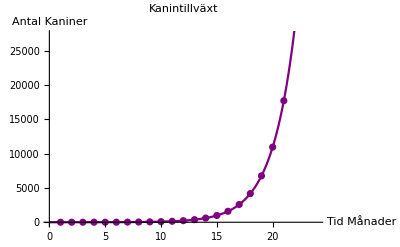
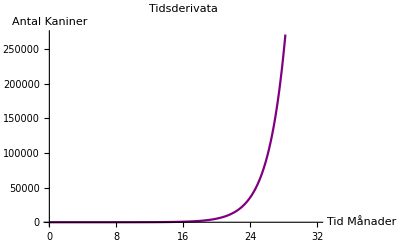
a) Svar: -Graphics-

b) Svar: Graf: -Graphics-
Diskution: {0.563413,0.911621,1.47503,2.38665,3.86169,6.24834,10.11,16.3584,26.4684,42.8268,69.2952,112.122,181.417,293.539,474.956,768.495,1243.45,2011.95,3255.4,5267.34,8522.74,13790.1,22312.8}, Grafen och talföljden visar att derivatan ökar exponetiellt. kaninpopulationen rör sig mot oändligheten. Realistiskt sätt så kommer tex mat och rovdjur göra så att populationen kommer att sluta växa och därmed avtar derivatan.

c) Svar: Graf: 
Diskussion: Giltighetsområdet för fibinaccis modell varierar av värdet på k enligt grafen ovan. Den gröna grafen representerar den realistiska tillväxten, den blå visualiserar den overkliga tillväxten och den gula visar Taket för kanin populationen.

## Kod

```mathematica
(*Uppgift 2, a*)
```

```mathematica
P[1]=1
```

1

```mathematica
P[2]=2
```

2

```mathematica
P[n_]:=P[n-2]+P[n-1]
```

```mathematica
nrpar=Table[P[n],{n,1,24}]
```

{1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025}

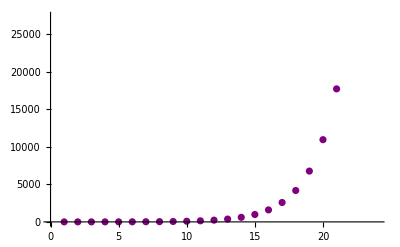

```mathematica
plotEtt=ListPlot[nrpar,PlotStyle->Purple]
```

```mathematica
{apar,bpar}={a,b}/.FindFit[nrpar,{a Exp[b t]},{a,b},t]
```

{0.723607,0.481212}

```mathematica
population[t_]=apar Exp[bpar t]
```

0.723607 ⅇ^(0.481212 t)

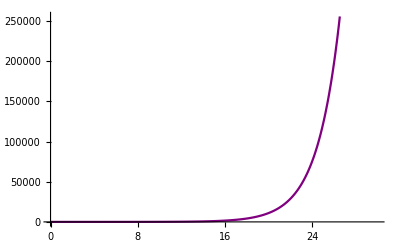

```mathematica
plottvå=Plot[population[t],{t,0,30}, PlotStyle->Purple]
```

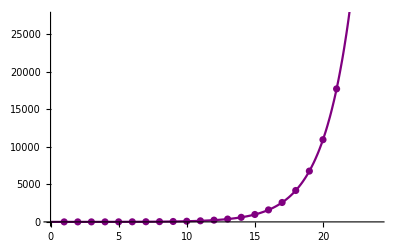

```mathematica
Show[plotEtt,plottvå]
```

```mathematica
Show[%87,AxesLabel->{HoldForm[Tid Månader],HoldForm[Antal Kaniner]},PlotLabel->HoldForm[Kanintillväxt],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
(*Uppgift 2, b,c,*)
```

```mathematica
populationDerivata[t_]=D[population [t],t]
```

0.348208 ⅇ^(0.481212 t)

```mathematica
Table[populationDerivata[t],{t,1,23}]
```

{0.563413,0.911621,1.47503,2.38665,3.86169,6.24834,10.11,16.3584,26.4684,42.8268,69.2952,112.122,181.417,293.539,474.956,768.495,1243.45,2011.95,3255.4,5267.34,8522.74,13790.1,22312.8}

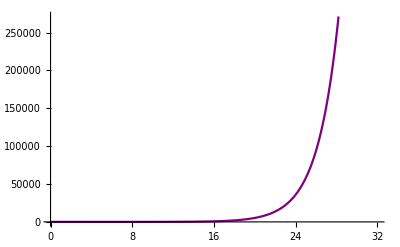

```mathematica
plottare = Plot[populationDerivata[t], {t,0,32}, PlotStyle->Purple]
```

```mathematica
Show[plottare,AxesLabel->{HoldForm[Tid Månader],HoldForm[Antal Kaniner]},PlotLabel->HoldForm[Tidsderivata],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
{populationDif1[t_]}=x[t]/. DSolve[{x'[t]==r x[t] (k-x[t])/k,x[0]==x0},x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{(ⅇ^(r t) k x0)/(k-x0+ⅇ^(r t) x0)}

```mathematica
populationDif2[t_]:=populationDif[t]/. {x0->apar,r->bpar}
```

```mathematica
Manipulate[Plot[{population[t],k, (ⅇ^(bpar t) k apar)/(k-apar+ⅇ^(bpar t) apar) },{t,0,30}],{k,1000,100000}]
```